```mathematica
Ibias={3,3,5,5,2.5}
(*input1[t_]:=1Sin[π t/400]HeavisideTheta[t-00.1]
inputAnti[t_]:=1Sin[(π (t-400) /400)]HeavisideTheta[t-00.1]
inputAdv[t_][Δ_]:=1Sin[(π (t-Δ) /400)]HeavisideTheta[t-00.1]
inputLag[t_]:=1Sin[(π (t+50) /400)]HeavisideTheta[t-00.1]*)

input1[t_][f_]:=DiracComb[f t/20]/40
inputAdv[t_][f_,Δ_]:=DiracComb[f(t-Δ)/20]/40


(*f1 = 3(*input corrisponding to 1*)
f2 = 3(*input corrisponding to 0*)
θ=40
input1[t_]:=f1 Iinj[100,300][t]+f1 Iinj[500,300][t]+f2 Iinj[900,300][t]
input2[t_]:=f1 Iinj[100+θ,300][t]+f2 Iinj[500+θ,300][t]+f1 Iinj[900+θ,300][t]
*)
time =1000
Fv[V_,W_][Ii_,k_,b_]:=-3V+((1/k)*V^2 +40+100b-W+Ii)
Fw[V_,W_][a_,b_]:=a (b(V)-W)
Iinj [start_,dur_][t_]:=HeavisidePi[(t-start)/dur-1/2]
T[x_]:=Transpose[x]
L[x_]:=Length[x]
(*base parameters of the neurons*)
k = 25
a =1/10.
b=.2
c= 10
d =.01
tau =10

(*synaptic weights*)
go=4
gee = 2
gei = 5
gie = -10
gii = -10

ClassicalRungeKuttaCoefficients[4,prec_]:=With[{amat={{1/2},{0,1/2},{0,0,1}},bvec={1/6,1/3,1/3,1/6},cvec={1/2,1/2,1}},N[{amat,bvec,cvec},prec]]
```

{3,3,5,5,2.5}

1000

25

0.1

0.2

10

0.01

10

4

2

5

-10

-10

```mathematica
Monitor[xDat=Table[
Ibias={q+e,e,2.5,2.5,2};
solAdvAND=NDSolve[
{(*neuron e1*)
Ve1'[t]==Fv[Ve1[t],We1[t]][Ibias[[1]],k,b]+input1[t][f]+gee Se2[t] +gie Si1[t]+Ibias[[1]],Ve1[0]==0,
We1'[t]==Fw[Ve1[t],We1[t]][a,b],We1[0]==6,
tau Se1'[t]== -Se1[t],Se1[0]==0,
WhenEvent[Ve1[t]==130,{Ve1[t]->c,We1[t]->We1[t]+d,Se1[t]->Se1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron e2*)
Ve2'[t]==Fv[Ve2[t],We2[t]][Ibias[[2]],k,b]+inputAdv[ t][f,Δ]+gee Se1[t] +gie Si2[t]+Ibias[[2]],Ve2[0]==0,
We2'[t]==Fw[Ve2[t],We2[t]][a,b],We2[0]==6,
tau Se2'[t]== -Se2[t],Se2[0]==0,
WhenEvent[Ve2[t]==130,{Ve2[t]->c,We2[t]->We2[t]+d,Se2[t]->Se2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron i1*)
Vi1'[t]==Fv[Vi1[t],Wi1[t]][Ibias[[3]],k,b]+input1[ t][f]+gii Si2[t]+gei Se1[t]+Ibias[[3]],Vi1[0]==0,
Wi1'[t]==Fw[Vi1[t],Wi1[t]][a,b],Wi1[0]==6,
tau Si1'[t]== -Si1[t],Si1[0]==0,
WhenEvent[Vi1[t]==130,{Vi1[t]->c,Wi1[t]->Wi1[t]+d,Si1[t]->Si1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuroni2*)
Vi2'[t]==Fv[Vi2[t],Wi2[t]][Ibias[[4]],k,b]+inputAdv[t][f,Δ]+gii Si1[t]+gei Se2[t]+Ibias[[4]],Vi2[0]==0,
Wi2'[t]==Fw[Vi2[t],Wi2[t]][a,b],Wi2[0]==6,
tau Si2'[t]== -Si2[t],Si2[0]==0,
WhenEvent[Vi2[t]==130,{Vi2[t]->c,Wi2[t]->Wi2[t]+d,Si2[t]->Si2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron out*)
Vo'[t]==Fv[Vo[t],Wo[t]][Ibias[[5]],k,b]+go Se1[t]+go Se2[t],Vo[0]==0,
Wo'[t]==Fw[Vo[t],Wo[t]][a,b],Wo[0]==6,
tau So'[t]== 0,So[0]==0,
WhenEvent[Vo[t]==130,{Vo[t]->c,Wo[t]->Wo[t]+d,So[t]->So[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"]},
{Ve1,We1,Se1,Ve2,We2,Se2,Vi1,Wi1,Si1,Vi2,Wi2,Si2,Vo,Wo,So},{t,0,time},Method->"BDF",Compiled->True];

SpikeCount=((So[400]/.solAdvAND)-(So[time]/.solAdvAND))[[1]],{Δ,-10,10,1},{f,1,2,.5},{e,-.5+.8,.7,.1},{q,1,2.5,.4}];,{f,Δ,e,q}]


NIMPout=Column[{
Plot[Vo[t]/.solAdvAND,{t,60,time},ImageSize->500,PlotRange->{0,140},PlotPoints->10000,PlotStyle->{{Thickness[.005],Black}},AspectRatio->(1/(2GoldenRatio)),Axes->None],
,Plot[{input1[t],inputAdv[t]},{t,60,time},PlotStyle->{{Thickness[.01],RGBColor[0,.2,.8]},{Thickness[.01],RGBColor[1,.6,0],Dashing[{.03,.06}]}},Exclusions->None,ImageSize->500,AspectRatio->(1/(4 GoldenRatio)),Axes->False]
}]
```

NDSolve::ndsz: At t == 640.27, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1000} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
ListDensityPlot[xDat,PlotRange->{All,-1},PlotLegends->Automatic,DataRange->{{1,4},{-400,400}}]
```

ListDensityPlot::arrayerr: {«1»} must be a valid array.

ListDensityPlot[{{{{0.,0.,0.,0.,-6.66134×10^-16},{0.,0.,0.,3.33067×10^-16,1.11022×10^-15},{0.,0.,2.22045×10^-16,4.44089×10^-16,-1.33227×10^-15},{0.,-5.55112×10^-16,6.66134×10^-16,-6.66134×10^-16,1.33227×10^-15},{-3.33067×10^-16,2.66454×10^-15,2.22045×10^-16,-1.11022×10^-15,1.11022×10^-15}},{{0.,0.,0.,0.,-1.22125×10^-15},{0.,0.,0.,3.33067×10^-16,1.11022×10^-15},{0.,0.,1.11022×10^-15,0.,-1.77636×10^-15},{0.,0.,1.55431×10^-15,3.10862×10^-15,-1.55431×10^-15},{3.33067×10^-16,3.55271×10^-15,1.33227×10^-15,0.,2.22045×10^-15}}},{{{0.,0.,0.,-10.,-1.11022×10^-16},{0.,0.,-10.,0.,1.33227×10^-15},{0.,-10.,3.33067×10^-16,1.33227×10^-15,8.88178×10^-16},{-10.,1.11022×10^-15,1.33227×10^-15,-8.88178×10^-16,8.88178×10^-16},{7.77156×10^-16,1.77636×10^-15,-8.88178×10^-16,-8.88178×10^-16,3.10862×10^-15}},{{0.,0.,0.,0.,-4.44089×10^-16},{0.,0.,0.,9.99201×10^-16,-3.33067×10^-15},{0.,0.,-4.44089×10^-16,1.9984×10^-15,1.33227×10^-15},{0.,1.44329×10^-15,4.44089×10^-15,7.10543×10^-15,1.9984×10^-15},{0.,7.54952×10^-15,-8.88178×10^-16,2.44249×10^-15,4.88498×10^-15}}},{{{0.,0.,0.,0.,-6.66134×10^-16},{0.,0.,0.,3.33067×10^-16,1.11022×10^-15},{0.,0.,2.22045×10^-16,4.44089×10^-16,-1.33227×10^-15},{0.,-5.55112×10^-16,6.66134×10^-16,-6.66134×10^-16,1.33227×10^-15},{-3.33067×10^-16,2.66454×10^-15,2.22045×10^-16,-1.11022×10^-15,1.11022×10^-15}},{{0.,0.,0.,0.,-1.22125×10^-15},{0.,0.,0.,3.33067×10^-16,1.11022×10^-15},{0.,0.,1.11022×10^-15,0.,-1.77636×10^-15},{0.,0.,1.55431×10^-15,3.10862×10^-15,-1.55431×10^-15},{3.33067×10^-16,3.55271×10^-15,1.33227×10^-15,0.,2.22045×10^-15}}},{{{0.,0.,0.,-10.,-1.11022×10^-16},{0.,0.,-10.,0.,1.33227×10^-15},{0.,-10.,3.33067×10^-16,1.33227×10^-15,8.88178×10^-16},{-10.,1.11022×10^-15,1.33227×10^-15,-8.88178×10^-16,8.88178×10^-16},{7.77156×10^-16,1.77636×10^-15,-8.88178×10^-16,-8.88178×10^-16,3.10862×10^-15}},{{0.,0.,0.,0.,4.44089×10^-16},{0.,0.,0.,-1.11022×10^-16,0.},{0.,0.,0.,9.10383×10^-15,1.55431×10^-15},{0.,1.11022×10^-15,2.88658×10^-15,5.77316×10^-15,1.11022×10^-15},{1.33227×10^-15,-4.44089×10^-15,4.44089×10^-15,8.88178×10^-16,4.21885×10^-15}}},{{{0.,0.,0.,0.,-6.66134×10^-16},{0.,0.,0.,3.33067×10^-16,1.11022×10^-15},{0.,0.,2.22045×10^-16,4.44089×10^-16,-1.33227×10^-15},{0.,-5.55112×10^-16,6.66134×10^-16,-6.66134×10^-16,1.33227×10^-15},{-3.33067×10^-16,2.66454×10^-15,2.22045×10^-16,-1.11022×10^-15,1.11022×10^-15}},{{0.,0.,0.,0.,-1.22125×10^-15},{0.,0.,0.,3.33067×10^-16,1.11022×10^-15},{0.,0.,1.11022×10^-15,0.,-1.77636×10^-15},{0.,0.,1.55431×10^-15,3.10862×10^-15,-1.55431×10^-15},{3.33067×10^-16,3.55271×10^-15,1.33227×10^-15,0.,2.22045×10^-15}}},{{{0.,0.,0.,-10.,-1.11022×10^-16},{0.,0.,-10.,0.,1.33227×10^-15},{0.,-10.,3.33067×10^-16,1.33227×10^-15,8.88178×10^-16},{-10.,1.11022×10^-15,1.33227×10^-15,-8.88178×10^-16,8.88178×10^-16},{7.77156×10^-16,1.77636×10^-15,-8.88178×10^-16,-8.88178×10^-16,3.10862×10^-15}},{{0.,0.,0.,0.,4.44089×10^-16},{0.,0.,0.,-1.11022×10^-16,0.},{0.,0.,0.,9.10383×10^-15,1.55431×10^-15},{0.,1.11022×10^-15,2.88658×10^-15,5.77316×10^-15,1.11022×10^-15},{1.33227×10^-15,-4.44089×10^-15,4.44089×10^-15,8.88178×10^-16,4.21885×10^-15}}},{{{0.,0.,0.,0.,-6.66134×10^-16},{0.,0.,0.,3.33067×10^-16,1.11022×10^-15},{0.,0.,2.22045×10^-16,4.44089×10^-16,-1.33227×10^-15},{0.,-5.55112×10^-16,6.66134×10^-16,-6.66134×10^-16,1.33227×10^-15},{-3.33067×10^-16,2.66454×10^-15,2.22045×10^-16,-1.11022×10^-15,1.11022×10^-15}},{{0.,0.,0.,0.,-1.22125×10^-15},{0.,0.,0.,3.33067×10^-16,1.11022×10^-15},{0.,0.,1.11022×10^-15,0.,-1.77636×10^-15},{0.,0.,1.55431×10^-15,3.10862×10^-15,-1.55431×10^-15},{3.33067×10^-16,3.55271×10^-15,1.33227×10^-15,0.,2.22045×10^-15}}},{{{0.,0.,0.,-10.,-1.11022×10^-16},{0.,0.,-10.,0.,1.33227×10^-15},{0.,-10.,3.33067×10^-16,1.33227×10^-15,8.88178×10^-16},{-10.,1.11022×10^-15,1.33227×10^-15,-8.88178×10^-16,8.88178×10^-16},{7.77156×10^-16,1.77636×10^-15,-8.88178×10^-16,-8.88178×10^-16,3.10862×10^-15}},{{0.,0.,0.,0.,8.88178×10^-16},{0.,0.,0.,1.33227×10^-15,2.66454×10^-15},{0.,0.,1.22125×10^-15,-1.55431×10^-15,2.66454×10^-15},{0.,-1.11022×10^-16,4.44089×10^-16,0.,6.66134×10^-16},{1.11022×10^-15,-6.66134×10^-15,5.77316×10^-15,-1.11022×10^-15,4.21885×10^-15}}},{{{0.,0.,0.,0.,-6.66134×10^-16},{0.,0.,0.,3.33067×10^-16,1.11022×10^-15},{0.,0.,2.22045×10^-16,4.44089×10^-16,-1.33227×10^-15},{0.,-5.55112×10^-16,6.66134×10^-16,-6.66134×10^-16,1.33227×10^-15},{-3.33067×10^-16,2.66454×10^-15,2.22045×10^-16,-1.11022×10^-15,1.11022×10^-15}},{{0.,0.,0.,0.,-1.22125×10^-15},{0.,0.,0.,3.33067×10^-16,1.11022×10^-15},{0.,0.,1.11022×10^-15,0.,-1.77636×10^-15},{0.,0.,1.55431×10^-15,3.10862×10^-15,-1.55431×10^-15},{3.33067×10^-16,3.55271×10^-15,1.33227×10^-15,0.,2.22045×10^-15}}}},PlotRange→{All,-1},PlotLegends→Automatic,DataRange→{{1,4},{-400,400}}]

```mathematica
time
```

1200

```mathematica
Dimensions[xDat]
(33+1)/2
```

{33,4}

17

```mathematica
xDat[[17]]
```

{0.,0.,0.,0.}

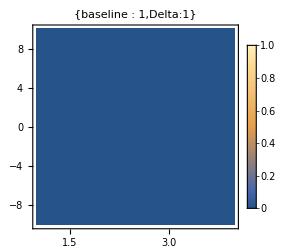
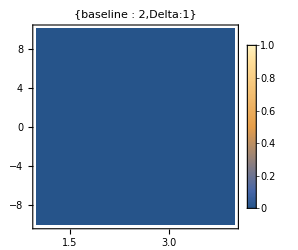
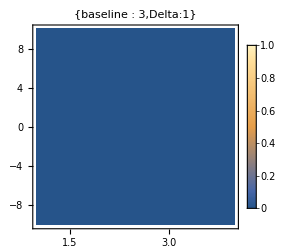
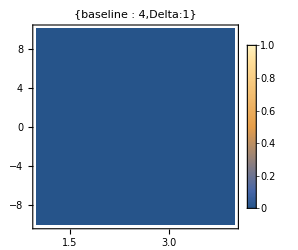
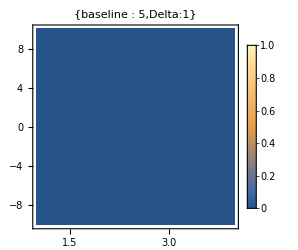
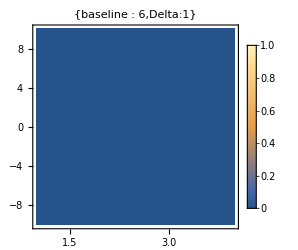
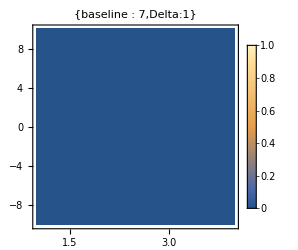
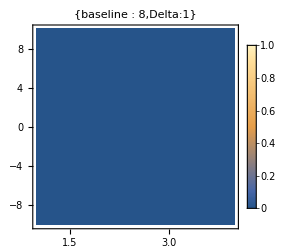
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
Row[Table[
Column[Table[ListDensityPlot[xDat[[All,All,i,j]],PlotRange->{All,-1},PlotLegends->Automatic,ImageSize->250,DataRange->{{1,4},{-10,10}},PlotLabel->{"baseline :  "<>ToString[i],"Delta:"<>ToString[j]}],{i,1,Length[xDat[[1,1]]]}]]
,{j,1,Length[xDat[[1,1,1]]]}]]
```